https://blog.wolfram.com/2015/02/27/find-waldo-faster/

#### Get feature’s position from image

```mathematica
wImage=Import["C:\\workspace\\workspace\\Wolfram\\Interests\\waldo.jpg"];
```

```mathematica
wImage
```

-Graphics-

```mathematica
Binarize[wImage]//ColorNegate//FillingTransform//Erosion[#,DiskMatrix[9]]&//SelectComponents[#,"Count",#<100&]&
```

-Graphics-

An alternate pattern to apply functions sequencially - //

```mathematica
FoldList[#2[#1]&,wImage,{
Binarize,
ColorNegate,
FillingTransform,
Erosion[#,DiskMatrix[9]]&,
SelectComponents[#,"Count",#<100&]&}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
spots=ComponentMeasurements[Last[%],"Centroid"][[All,2]];
Short[spots]
```

{{44.7,554.},«66»,{390.738,23.119}}

```mathematica
Show[wImage,Graphics[{Blue,Thickness[.005],Circle[#,15]&/@spots}]]
```

-Graphics-

```mathematica
book=spots 20/First@ImageDimensions[wImage];
Short[book]
```

{{0.971739,12.0435},{19.4848,12.},«65»,{8.49431,0.502588}}

```mathematica
strip[a_]:=ImplicitRegion[a<y≤a+1.5&&0<x<20,{x,y}];
```

```mathematica
scan=Table[{n,100Count[RegionMember[strip[n],book],True]/68.},{n,0,11,.2}]
```

{{0.,4.41176},{0.2,5.88235},{0.4,5.88235},{0.6,8.82353},{0.8,8.82353},{1.,10.2941},{1.2,11.7647},{1.4,11.7647},{1.6,14.7059},{1.8,17.6471},{2.,17.6471},{2.2,19.1176},{2.4,20.5882},{2.6,22.0588},{2.8,23.5294},{3.,23.5294},{3.2,22.0588},{3.4,19.1176},{3.6,14.7059},{3.8,13.2353},{4.,11.7647},{4.2,11.7647},{4.4,8.82353},{4.6,7.35294},{4.8,8.82353},{5.,7.35294},{5.2,7.35294},{5.4,10.2941},{5.6,10.2941},{5.8,13.2353},{6.,17.6471},{6.2,17.6471},{6.4,19.1176},{6.6,22.0588},{6.8,23.5294},{7.,23.5294},{7.2,23.5294},{7.4,19.1176},{7.6,14.7059},{7.8,13.2353},{8.,13.2353},{8.2,11.7647},{8.4,7.35294},{8.6,8.82353},{8.8,10.2941},{9.,11.7647},{9.2,11.7647},{9.4,11.7647},{9.6,8.82353},{9.8,10.2941},{10.,7.35294},{10.2,7.35294},{10.4,5.88235},{10.6,5.88235},{10.8,5.88235},{11.,5.88235}}

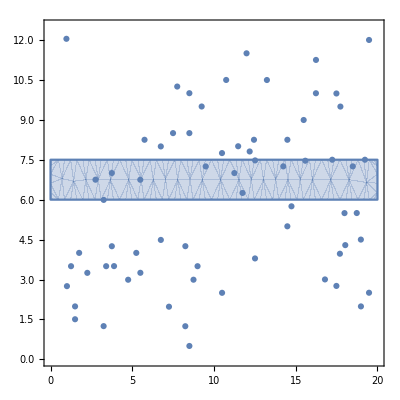
-Graphics--Graphics-

```mathematica
Row[{
ListLinePlot[scan,
PlotTheme->"Marketing",
Frame->True,
AspectRatio->1,
Epilog->{White,Thickness[.03],
Line[{{6,0},{6,25}}]}],
Show[
RegionPlot[
strip[6]],
ListPlot[book],
PlotRange->{{0,20},{0,12.5}}]}]
```

```mathematica
Reverse@SortBy[scan,Last]
```

{{7.2,23.5294},{7.,23.5294},{6.8,23.5294},{3.,23.5294},{2.8,23.5294},{6.6,22.0588},{3.2,22.0588},{2.6,22.0588},{2.4,20.5882},{7.4,19.1176},{6.4,19.1176},{3.4,19.1176},{2.2,19.1176},{6.2,17.6471},{6.,17.6471},{2.,17.6471},{1.8,17.6471},{7.6,14.7059},{3.6,14.7059},{1.6,14.7059},{8.,13.2353},{7.8,13.2353},{5.8,13.2353},{3.8,13.2353},{9.4,11.7647},{9.2,11.7647},{9.,11.7647},{8.2,11.7647},{4.2,11.7647},{4.,11.7647},{1.4,11.7647},{1.2,11.7647},{9.8,10.2941},{8.8,10.2941},{5.6,10.2941},{5.4,10.2941},{1.,10.2941},{9.6,8.82353},{8.6,8.82353},{4.8,8.82353},{4.4,8.82353},{0.8,8.82353},{0.6,8.82353},{10.2,7.35294},{10.,7.35294},{8.4,7.35294},{5.2,7.35294},{5.,7.35294},{4.6,7.35294},{11.,5.88235},{10.8,5.88235},{10.6,5.88235},{10.4,5.88235},{0.4,5.88235},{0.2,5.88235},{0.,4.41176}}

```mathematica
100 Count[RegionMember[strip[#],book],True]/68.&/@{3,7}//Total
```

47.0588

```mathematica
tour=FindShortestTour[book]
```

{100.57,{1,30,33,16,19,14,7,8,11,15,27,22,31,34,25,21,17,20,5,3,6,13,9,4,2,10,12,23,29,37,40,61,64,58,55,47,42,38,24,26,18,28,36,39,48,60,68,67,63,57,52,44,41,46,54,56,66,65,62,59,49,45,53,50,51,43,35,32,1}}

```mathematica
order=book[[Last[tour]]];
```

```mathematica
SmoothDensityHistogram[book,{1.5,"Cosine"},
Mesh->15,
Frame->False,
AspectRatio->Automatic,
ColorFunction->"RedBlueTones",
MeshStyle->Directive[Gray,Dashed],
PlotRange->{{0,20},{0,12.5}},
Epilog->{
{Opacity[.5],White,Thickness[.03],
BSplineCurve[Most[order],SplineClosed->True]},
{PointSize[.01],Point[book]},Line[order]}]
```

-Graphics-

```mathematica
bookS=Rest@Sort[book];
tourS=FindShortestTour[bookS,1,67];
orderS=bookS[[Last@tourS]];
```

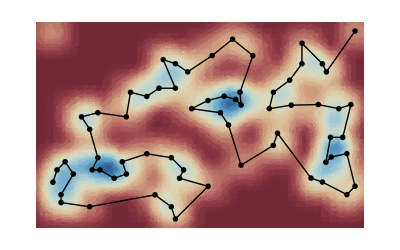

```mathematica
SmoothDensityHistogram[book,{1.5,"Cosine"},
Mesh->15,
Frame->False,
AspectRatio->Automatic,
ColorFunction->"RedBlueTones",
MeshStyle->Directive[Gray,Dashed],
PlotRange->{{0,20},{0,12.5}},
Epilog->{
{PointSize[.01],Point[bookS]},Line[orderS]}]
```

```mathematica
First@tourS
```

88.5276

```mathematica
distance=Table[EuclideanDistance[a,b],{a,bookS},{b,bookS}];
```

A pattern to apply a list to a function that accepts sequence.

```mathematica
path=Last[tourS]
distance[[##]]&@@@Partition[path,2,1]//Total
```

{1,2,5,6,4,3,8,21,24,28,34,29,30,25,20,15,17,14,13,10,11,9,7,12,16,18,19,22,26,23,27,31,35,39,44,41,43,40,37,33,32,36,38,42,46,48,53,55,64,66,63,60,57,59,62,65,61,54,50,45,47,49,51,52,56,58,67}

88.5276